```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=ReadList["plot2pi.txt",{Number,Number}];
Fq2π100=ReadList["plot2pi_100.txt",{Number,Number}];
Fq2π1000=ReadList["plot2pi_1000.txt",{Number,Number}];
Fq2π10000=ReadList["plot210000pi.txt",{Number,Number}];
```

## Initial Tau lepton calculations for constants

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
HT;


m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
BrNorm=0.2549;
```

```mathematica
Clear[Br]
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π][q2];
(*Decay to 2π*)
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.352821

1.

```mathematica
Clear[Br]
dΓ2π100= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π100][q2];
(*Decay to 2π*)
Γ2π100=NIntegrate[dΓ2π100, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π100/Γτ;
Const2π100=BrNorm/Br
Γ2π100=Const2π100*NIntegrate[dΓ2π100, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π100/Γτ;
Error=Br/BrNorm
```

0.352821

1.

```mathematica
Clear[Br];
dΓ2π1000= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π1000][q2];
(*Decay to 2π*)
Γ2π1000=NIntegrate[dΓ2π1000, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π1000/Γτ;
Const2π1000=BrNorm/Br
Γ2π1000=Const2π1000*NIntegrate[dΓ2π1000, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π1000/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
Clear[Br];
dΓ2π10000= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π10000][q2];
(*Decay to 2π*)
Γ2π10000=NIntegrate[dΓ2π10000, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π10000/Γτ;
Const2π10000=BrNorm/Br
Γ2π10000=Const2π10000*NIntegrate[dΓ2π10000, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π10000/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
Clear[Br];
BWr[qsum_]:=Module[{ret,mRho,gammaRho,mRhopr,gammaRhopr,beta,m1,m2,mQ2,dRho,pPiRho,dRhopr,pPiRhopr,dQ,pPiQ,BRhoDem,BRho,BRhoprDem,BRhopr},mRho=0.775;
gammaRho=0.149;
mRhopr=1.364;
gammaRhopr=0.400;
beta=-0.108;
m1=0.13957018;m2=0.13957018;
mQ2=qsum*qsum;(*?*)dRho=mRho*mRho-m1*m1-m2*m2;
pPiRho=(1.0/mRho)*Sqrt[(dRho*dRho)/4.0-m1*m1*m2*m2];
dRhopr=mRhopr*mRhopr-m1*m1-m2*m2;
pPiRhopr=(1.0/mRhopr)*Sqrt[(dRhopr*dRhopr)/4.0-m1*m1*m2*m2];
dQ=mQ2-m1*m1-m2*m2;
pPiQ=(1.0/Sqrt[mQ2])*Sqrt[(dQ*dQ)/4.0-m1*m1*m2*m2];
gammaRho=gammaRho*mRho/Sqrt[mQ2]*Power[(pPiQ/pPiRho),3];
BRhoDem=mRho*mRho-mQ2+I*(-1.0*mRho*gammaRho);
BRho=mRho*mRho/BRhoDem;
gammaRhopr=gammaRhopr*mRhopr/Sqrt[mQ2]*Power[(pPiQ/pPiRhopr),3];
BRhoprDem=mRhopr*mRhopr-mQ2+I*(-1.0*mRho*gammaRhopr);
BRhopr=mRhopr*mRhopr/BRhoprDem;
ret=(BRho+beta*BRhopr)/(1+beta);
Return[ret]]
ret1=BWr[q]*ComplexConjugate[BWr[q]];
mpi=0.13957018;
ret2=ret1*(4*mpi^2-q*q);
ret3=ret2/(-3 q*q);
λr=Sqrt[(q^2-4 mpi^2)/q^2];
ret4=ret3*λr/(8 π);
ret5=ret4/.{q->Sqrt[q2]};

Fq2πb=ret5;
dΓ2πb=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2πb;
Γ2πb=NIntegrate[dΓ2πb,{q2,4 mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
BrNorm=0.2549;
Const2πb=BrNorm/Br
Γ2πb=Const2πb*NIntegrate[dΓ2πb,{q2,4 mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
Error=Br/BrNorm
```

0.353281+6.26928×10^-19 ⅈ

1.+0. ⅈ

## Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π*Interpolation[Fq2π][m232];
dΓ2π100:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π100*Interpolation[Fq2π100][m232];
dΓ2π1000:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π1000*Interpolation[Fq2π1000][m232];
dΓ2π10000:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π10000*Interpolation[Fq2π10000][m232];
ret6=ret4/.{q->Sqrt[m232]};
dΓ2πbefore:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Re[Const2πb]*ret6;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
testresult={};
AppendTo[testresult,{"in","out","l nul" ,"2 pi", "2pi_100","2pi_1000"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,9mπ^2,(m1-m2)^2}];
Γ2π100=NIntegrate[dΓ2π100, {m232,9mπ^2,(m1-m2)^2}];
Γ2π1000=NIntegrate[dΓ2π1000, {m232,9mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Floor[Chop[Γl1/fullΓ],-0.00001]*100, Floor[Chop[Γ2π100/fullΓ],-0.00001]*100, Floor[Chop[Γ2π1000/fullΓ],-0.00001]*100, Floor[Chop[Γ2π/fullΓ],-0.00001]*100}];
testresult
```

(in | out | l nul | 2 pi
\Omega_{cc}^{+} | \Omega_{c}^{0} | 6.661 | 16.796)

```mathematica
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"a_{1}"]&]][[1]]["width"]
```

Missing[PartAbsent,1][width]

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","Vckm","l nul","pi" ,"rho/2pi","2pi_100/2pi_before", "2pi_1000/2pi_before" 
, "2pi_10000/2pi_before"
}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ2π100=NIntegrate[dΓ2π100, {m232,4mπ^2,(m1-m2)^2}];
Γ2π1000=NIntegrate[dΓ2π1000, {m232,4mπ^2,(m1-m2)^2}];
Γ2π10000=NIntegrate[dΓ2π10000, {m232,4mπ^2,(m1-m2)^2}];
Γ2πbefore=Re[NIntegrate[dΓ2πbefore, {m232,4mπ^2,(m1-m2)^2}]];
AppendTo[result,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π100/Γ2πbefore],-0.0000001], Floor[Chop[Γ2π1000/Γ2πbefore],-0.0000001]
 , Floor[Chop[Γ2π10000/Γ2πbefore],-0.0000001]
}];
,{dec,decays}];
result
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.04309}. NIntegrate obtained TraditionalForm`6.199949246656747`*^-14 and TraditionalForm`2.7953540267495105`*^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`18 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m122, m232} = TraditionalForm`{0.468141, 0.0332227}. NIntegrate obtained TraditionalForm`6.200280512010538`*^-14 and TraditionalForm`5.231484967839733`*^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.0429364}. NIntegrate obtained TraditionalForm`6.139831083689381`*^-14 and TraditionalForm`2.321958443411979`*^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

(in | out | Vckm | l nul | pi | rho/2pi | 2pi_100/2pi_before | 2pi_1000/2pi_before | 2pi_10000/2pi_before
\Xi_{cc}^{++} | \Lambda_{c}^{+} | c→d | 0.4936 | 0.377359 | 1.15032 | 1.00003 | 1.00003 | 1.00003
\Xi_{cc}^{++} | \Sigma_{c}^{+} | c→d | 0.4503 | 0.301942 | 1.16641 | 1.00005 | 1.0002 | 1.0002
\Xi_{cc}^{++} | \Xi_{c}^{+} | c→s | 4.9858 | 8.30163 | 1.22609 | 1.00014 | 0.999724 | 0.999724
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | c→s | 5.975 | 6.92904 | 1.24902 | 1.00027 | 0.999994 | 0.999994
\Xi_{cc}^{+} | \Sigma_{c}^{0} | c→d | 0.2988 | 0.201094 | 1.16699 | 1.00005 | 1.00019 | 1.00019
\Xi_{cc}^{+} | \Xi_{c}^{0} | c→s | 1.6513 | 2.74944 | 1.22609 | 1.00014 | 0.999724 | 0.999724
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | c→s | 1.984 | 2.30995 | 1.24976 | 1.00027 | 0.999992 | 0.999992
\Omega_{cc}^{+} | \Xi_{c}^{0} | c→d | 0.2079 | 0.293426 | 1.21729 | 1.00013 | 0.999813 | 0.999813
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | c→d | 0.2492 | 0.244044 | 1.23135 | 1.00023 | 1.00007 | 1.00007
\Omega_{cc}^{+} | \Omega_{c}^{0} | c→s | 6.6604 | 11.1885 | 1.33522 | 1.00063 | 0.999715 | 0.999715
\Xi_{bb}^{0} | \Sigma_{b}^{+} | b→u | 0.0043 | 1.43×10^-6 | 1.02343 | 0.999906 | 1.0002 | 1.0002
\Xi_{bb}^{0} | \Xi_{bc}^{+} | b→c | 2.5911 | 0.00347432 | 1.05087 | 0.999929 | 1.00014 | 1.00014
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | b→c | 1.1503 | 0.00062621 | 1.02257 | 0.999906 | 1.0002 | 1.0002
\Xi_{bb}^{-} | \Lambda_{b}^{0} | b→u | 0.0011 | 8.3×10^-7 | 1.04536 | 0.99992 | 1.00015 | 1.00015
\Xi_{bb}^{-} | \Sigma_{b}^{0} | b→u | 0.0022 | 7.2×10^-7 | 1.02344 | 0.999906 | 1.0002 | 1.0002
\Xi_{bb}^{-} | \Xi_{bc}^{0} | b→c | 2.6207 | 0.00348729 | 1.05084 | 0.999929 | 1.00014 | 1.00014
\Xi_{bb}^{-} | \Xi_{bc}^{\prime0} | b→c | 1.1556 | 0.0006233 | 1.02254 | 0.999906 | 1.0002 | 1.0002
\Omega_{bb}^{-} | \Xi_{b}^{0} | b→u | 0.002 | 1.64×10^-6 | 1.04549 | 0.99992 | 1.00015 | 1.00015
\Omega_{bb}^{-} | \Xi_{b}^{\prime0} | b→u | 0.0044 | 1.44×10^-6 | 1.02351 | 0.999906 | 1.0002 | 1.0002
\Omega_{bb}^{-} | \Omega_{bc}^{0} | b→c | 4.8074 | 0.00702028 | 1.05142 | 0.999929 | 1.00014 | 1.00014
\Omega_{bb}^{-} | \Omega_{bc}^{\prime0} | b→c | 2.1266 | 0.00125917 | 1.02228 | 0.999904 | 1.0002 | 1.0002
\Xi_{bc}^{+} | \Lambda_{b}^{0} | c→d | 0.2234 | 0.0438204 | 1.17123 | 1.00008 | 0.999997 | 0.999997
\Xi_{bc}^{+} | \Sigma_{b}^{0} | c→d | 0.1483 | 0.0305531 | 1.21443 | 1.00016 | 1.0001 | 1.0001
\Xi_{bc}^{+} | \Xi_{b}^{0} | c→s | 2.3 | 0.927201 | 1.23671 | 1.00015 | 0.999697 | 0.999697
\Xi_{bc}^{0} | \Sigma_{b}^{-} | c→d | 0.1121 | 0.0232861 | 1.21575 | 1.00016 | 1.0001 | 1.0001
\Xi_{bc}^{0} | \Xi_{b}^{-} | c→s | 0.8684 | 0.352921 | 1.23739 | 1.00015 | 0.999692 | 0.999692
\Omega_{bc}^{0} | \Xi_{b}^{-} | c→d | 0.2542 | 0.0383789 | 1.15362 | 1.00003 | 1.00004 | 1.00004
\Omega_{bc}^{0} | \Omega_{b}^{-} | c→s | 6.0272 | 1.25182 | 1.22187 | 1.00018 | 1.00007 | 1.00007
\Xi_{bc}^{+} | \Sigma_{c}^{++} | b→u | 0.0035 | 2.63×10^-6 | 1.02768 | 0.999918 | 1.00018 | 1.00018
\Xi_{bc}^{+} | \Xi_{cc}^{++} | b→c | 1.5843 | 0.00802878 | 1.05773 | 0.999935 | 1.00012 | 1.00012
\Xi_{bc}^{0} | \Lambda_{c}^{+} | b→u | 0.0003 | 5.1×10^-7 | 1.04859 | 0.999928 | 1.00014 | 1.00014
\Xi_{bc}^{0} | \Sigma_{c}^{+} | b→u | 0.0007 | 5.×10^-7 | 1.02768 | 0.999918 | 1.00018 | 1.00018
\Xi_{bc}^{0} | \Xi_{cc}^{+} | b→c | 0.6027 | 0.00305399 | 1.05773 | 0.999935 | 1.00012 | 1.00012
\Omega_{bc}^{0} | \Xi_{c}^{+} | b→u | 0.0005 | 9.4×10^-7 | 1.04793 | 0.999926 | 1.00014 | 1.00014
\Omega_{bc}^{0} | \Omega_{cc}^{+} | b→c | 1.8684 | 0.00663499 | 1.05554 | 0.999934 | 1.00013 | 1.00013)

```mathematica
dΓ2πbefore
```

2.68889×10^-14 √(1-0.076016 (√m232+2.486)^2) √(1-0.076016 (2.486-√m232)^2) (24.8304 m232 (-0.0116351/(0.198912 m232^2+0.381039 m232+1)-0.0489898/(0.187778 m232^2-0.600925 m232+1)) (0.379671/(0.0160788 m232^2-0.214335 m232+1)-0.12125/(0.010798 m232^2-0.226757 m232+1)) (37.3688-m232)-133.031 m232 (0.491123/(0.0450092 m232^2-0.381039 m232+1)-0.479488/(0.0385705 m232^2-0.358564 m232+1)) (0.452543/(0.0577662 m232^2-0.400577 m232+1)+0.461729/(0.0218107 m232^2-0.295369 m232+1)) (1.30188-m232)+13.1551 (-2 m232^2+60.2805 m232+13.1551 (m232-12.3604)+211.252) (0.379671/(0.0160788 m232^2-0.214335 m232+1)-0.12125/(0.010798 m232^2-0.226757 m232+1))^2+13.1551 (-2 m232^2-47.9201 m232+13.1551 (m232-12.3604)+211.252) (0.452543/(0.0577662 m232^2-0.400577 m232+1)+0.461729/(0.0218107 m232^2-0.295369 m232+1))^2-m232 ((m232^2+60.2805 m232+13.1551 (m232+24.7208)-422.504) (0.491123/(0.0450092 m232^2-0.381039 m232+1)-0.479488/(0.0385705 m232^2-0.358564 m232+1))^2+(m232^2-47.9201 m232+13.1551 (m232+24.7208)-422.504) (-0.0116351/(0.198912 m232^2+0.381039 m232+1)-0.0489898/(0.187778 m232^2-0.600925 m232+1))^2)) Real[0.353281+6.26928×10^-19 ⅈ] Real[-1/m2320.016669 √((m232-0.0779193)/m232) (0.600625/(-((0.+1.8945 ⅈ) (0.25 (m232-0.0389597)^2-0.000379464)^(3/2))/m232^2-m232+0.600625)-0.200934/(-((0.+1.42133 ⅈ) (0.25 (m232-0.0389597)^2-0.000379464)^(3/2))/m232^2-m232+1.8605)) (0.600625/(((0.+1.8945 ⅈ) (0.25 (m232-0.0389597)^2-0.000379464)^(3/2))/m232^2-m232+0.600625)-0.200934/(((0.+1.42133 ⅈ) (0.25 (m232-0.0389597)^2-0.000379464)^(3/2))/m232^2-m232+1.8605)) (0.0779193-m232)]

```mathematica
Interpolation[Fq2π10000,1.34]
```

0.0165833

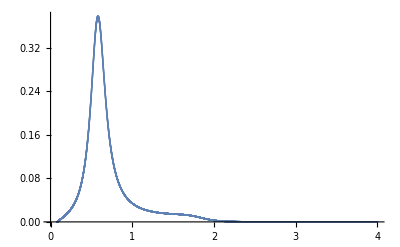

```mathematica
ListPlot[Fq2π10000, PlotRange->All]
```

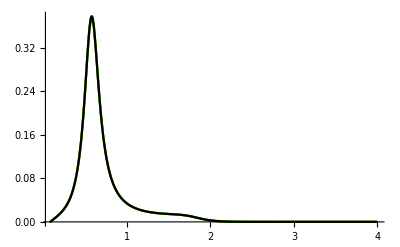

```mathematica
Show[ListPlot[Fq2π100, Joined -> True, PlotRange->All, PlotStyle-> Red],ListPlot[Fq2π1000, Joined -> True, PlotRange->All, PlotStyle-> Green], ListPlot[Fq2π10000, Joined -> True, PlotRange->All, PlotStyle-> Black]]
```

```mathematica
in="\\Xi_{bc}^{0}";
out="\\Sigma_{c}^{+}";
testresult={};
AppendTo[testresult,{"in","out","l nul" ,"pi","rho", "2pi", "2pibefore"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*a1*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*a1*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ2πbefore=NIntegrate[dΓ2πbefore, {m232,4mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Floor[Chop[Γl1/fullΓ],-0.00001]*100,Floor[Chop[Γπ/fullΓ],-0.00001]*100,Floor[Chop[Γρ/fullΓ],-0.00001]*100, Floor[Chop[Γ2π/fullΓ],-0.00001]*100,Floor[Chop[Γ2πbefore/fullΓ],-0.00001]*100}];
testresult
```

NIntegrate::inumr: The integrand TraditionalForm`8.85293×10^-23\ √1 - 0.020919\ (2.453  - Power[« 2 »])^2\ √1 - 0.020919\ (2.453  + √m232)^2\ (« 1 »)\ (1 + 0.638442\ q2)\ (-0.0784 + q2)^2/(0.0130642  + (-0.568655 + q2)^2)\ q2^2 has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand TraditionalForm`8.85293×10^-23\ √1 - 0.020919\ (2.453  - Power[« 2 »])^2\ √1 - 0.020919\ (2.453  + √m232)^2\ (« 1 »)\ (1 + 0.638442\ q2)\ (-0.0784 + q2)^2/(0.0130642  + (-0.568655 + q2)^2)\ q2^2 has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

(in | out | l nul | pi | rho | 2pi | 2pibefore
\Xi_{bc}^{0} | \Sigma_{c}^{+} | 0.001 | 0.001 | 0.001 | 0.001 | 100 Floor[1.41432×10^11 NIntegrate[dΓ2πbefore,{m232,4 mπ^2,(m1-m2)^2}],-0.00001])

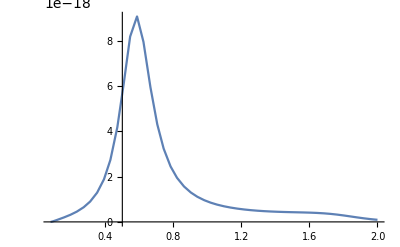

```mathematica
Plot[dΓ2π,{m232, 4 mpi^2, 2}, PlotRange-> All]
```

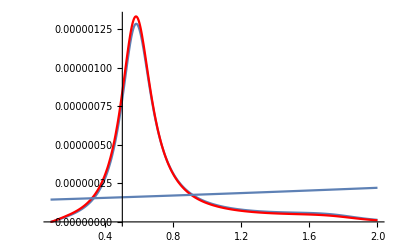

```mathematica
Show[Plot[dΓ2π/fullΓ,{m232, 4 mpi^2, 2}, PlotRange-> All],Plot[Fq2π/100000,{m232, 4 mpi^2, 2}, PlotRange-> All, PlotStyle->Red], Plot[dΓl/fullΓ,{m232,  4 mpi^2, 2}, PlotRange-> All],PlotRange-> All]
```

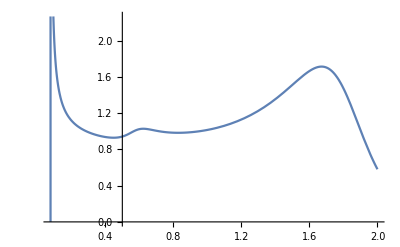

```mathematica
Plot[Fq2π/Fq2πbefore, {m232, 4mpi^2, 2}]
```

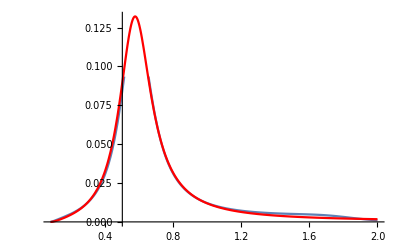

```mathematica
Show[Plot[Fq2π,{m232, 4mpi^2, 2}],Plot[Fq2πbefore,{m232, 4mpi^2, 2},PlotStyle-> Red], PlotRange-> All]
```